```mathematica
outputdir="/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/";
```

{{:0,:1,:2},{3.,0,0},{2.9,0,0},{2.8,0,0},{2.7,0,0},{2.6,0,0},{2.5,0,0},{2.4,0,0},{2.3,0,0},{2.2,0,0},{2.1,0,0},{2.,0,0},{1.9,0,0},{1.8,0,0},{1.7,0,0},{1.6,0,0},{1.5,0,0},{1.4,0,0},{1.3,0,0},{1.2,0,0},{1.1,0,0},{1.,0,0}}

{{3.,0,0},{2.9,0,0},{2.8,0,0},{2.7,0,0},{2.6,0,0},{2.5,0,0},{2.4,0,0},{2.3,0,0},{2.2,0,0},{2.1,0,0},{2.,0,0},{1.9,0,0},{1.8,0,0},{1.7,0,0},{1.6,0,0},{1.5,0,0},{1.4,0,0},{1.3,0,0},{1.2,0,0},{1.1,0,0},{1.,0,0}}

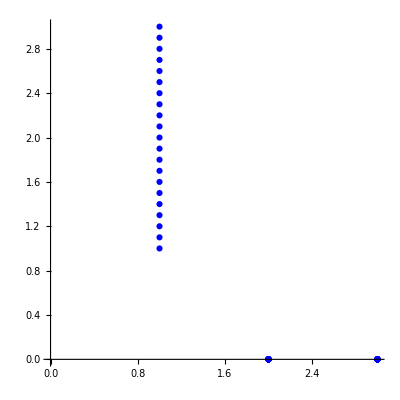

21

```mathematica
tabve=Import["/Users/michelecastellana/Documents/finite_elements/generate_mesh/1d/line/solution/vertices.csv"]
tabve=Table[tabve[[i]],{i,2,Length[tabve]}]
ListPlot[tabve,PlotStyle->Blue,AspectRatio->1]
Length[tabve]
```

```mathematica
(*write v from ODE to csv file*)
```

```mathematica
tabv=Table[Flatten[{{v[x],0,0}/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]}],{i,1,Length[tabve]}];
PrependTo[tabv,{"f:0","f:1","f:2",":0",":1",":2"}]
```

```mathematica
Export[outputdir<>"v.csv",tabv]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/v.csv

```mathematica
(*write w from ODE to csv file*)
```

```mathematica
tabw=Table[{w[x]/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]},{i,1,Length[tabve]}];
PrependTo[tabw,{"f",":0",":1",":2"}]
```

{{f,:0,:1,:2},{0,3.,0,0},{0,2.9,0,0},{0,2.8,0,0},{0,2.7,0,0},{0,2.6,0,0},{0,2.5,0,0},{0,2.4,0,0},{0,2.3,0,0},{0,2.2,0,0},{0,2.1,0,0},{0,2.,0,0},{0,1.9,0,0},{0,1.8,0,0},{0,1.7,0,0},{0,1.6,0,0},{0,1.5,0,0},{0,1.4,0,0},{0,1.3,0,0},{0,1.2,0,0},{0,1.1,0,0},{0,1.,0,0}}

```mathematica
Export[outputdir<>"w.csv",tabw]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/w.csv

```mathematica
(*write σ from ODE to csv file*)
```

```mathematica
tabσ=Table[{σ[x]/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]},{i,1,Length[tabve]}];
PrependTo[tabσ,{"f",":0",":1",":2"}]
```

{{f,:0,:1,:2},{1,3.,0,0},{1,2.9,0,0},{1,2.8,0,0},{1,2.7,0,0},{1,2.6,0,0},{1,2.5,0,0},{1,2.4,0,0},{1,2.3,0,0},{1,2.2,0,0},{1,2.1,0,0},{1,2.,0,0},{1,1.9,0,0},{1,1.8,0,0},{1,1.7,0,0},{1,1.6,0,0},{1,1.5,0,0},{1,1.4,0,0},{1,1.3,0,0},{1,1.2,0,0},{1,1.1,0,0},{1,1.,0,0}}

```mathematica
Export[outputdir<>"sigma.csv",tabσ]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/sigma.csv

```mathematica
(*write ψ from ODE to csv file*)
```

```mathematica
tabψ=Table[{ψ[x]/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]},{i,1,Length[tabve]}];
PrependTo[tabψ,{"f",":0",":1",":2"}]
```

{{f,:0,:1,:2},{2.,3.,0,0},{1.83004,2.9,0,0},{1.63761,2.8,0,0},{1.4263,2.7,0,0},{1.20081,2.6,0,0},{0.966854,2.5,0,0},{0.730793,2.4,0,0},{0.49916,2.3,0,0},{0.278131,2.2,0,0},{0.0730886,2.1,0,0},{-0.111654,2.,0,0},{-0.272926,1.9,0,0},{-0.408598,1.8,0,0},{-0.51739,1.7,0,0},{-0.59863,1.6,0,0},{-0.652026,1.5,0,0},{-0.677485,1.4,0,0},{-0.674994,1.3,0,0},{-0.644551,1.2,0,0},{-0.586181,1.1,0,0},{-0.5,1.,0,0}}

```mathematica
Export[outputdir<>"psi.csv",tabψ]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/psi.csv

```mathematica
(*write μ from ODE to csv file*)
```

```mathematica
tabμ=Table[{H[x]/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]},{i,1,Length[tabve]}];
PrependTo[tabμ,{"f",":0",":1",":2"}]
```

{{f,:0,:1,:2},{-0.789084,3.,0,0},{-0.908473,2.9,0,0},{-1.01281,2.8,0,0},{-1.09639,2.7,0,0},{-1.15371,2.6,0,0},{-1.1805,2.5,0,0},{-1.17462,2.4,0,0},{-1.13653,2.3,0,0},{-1.06925,2.2,0,0},{-0.977579,2.1,0,0},{-0.867217,2.,0,0},{-0.74374,1.9,0,0},{-0.611936,1.8,0,0},{-0.475448,1.7,0,0},{-0.336722,1.6,0,0},{-0.197168,1.5,0,0},{-0.0574222,1.4,0,0},{0.0823386,1.3,0,0},{0.222072,1.2,0,0},{0.361543,1.1,0,0},{0.5,1.,0,0}}

```mathematica
Export[outputdir<>"mu.csv",tabμ]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/mu.csv

```mathematica
(*write X from ODE to csv file*)
```

```mathematica
tabX=Table[Flatten[{{X1[x],X2[x],0}/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]}],{i,1,Length[tabve]}];
PrependTo[tabX,{"f:0","f:1","f:2",":0",":1",":2"}]
```

```mathematica
Export[outputdir<>"X.csv",tabX]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/X.csv